# TrueSkill player Ranking

```mathematica
Quit[]
```

```mathematica
SetDirectory@NotebookDirectory[];
<<wlPython`
```

# Versions
 - 1.0 (2015-07-XX)  --  Initial version 
 - 2.0 (2015-12-17)  -- changed the way python is executed to make it efficient
 - 2.1 (2015-12-17)  -- changed TS engine tau parameter to make it more flexible

## step 1: get the data

```mathematica
singlesRaw = Import["https://docs.google.com/spreadsheet/ccc?key=1wPZclPCCTRxLpADlaru2yhlssleeLQSe7MfPSpzuY34&output=csv"];

threadSingles[line_]:= <|
"Date" -> DateObject[line⟦1⟧, TimeZone->0],
"RedName" -> line⟦2⟧,
"RedScore" -> line⟦3⟧,
"BlueName" -> line⟦4⟧,
"BlueScore" -> line⟦5⟧  |>

singles = Dataset [threadSingles /@ singlesRaw⟦2;;⟧];
```

```mathematica
(*filter out names that are odd*)
bannedNames = {"aaaa3"};
singles = singles[Select[ !MemberQ[bannedNames,#RedName] && !MemberQ[bannedNames,#BlueName]&]];
```

```mathematica
(*testing*)
(* singles = Dataset [
threadSingles /@ (singlesRaw⟦2;;⟧ ~ Join ~ Table[{"2015-10-10", "ufk20", 10, "eh443", 1,""}, {1}])
];

*)
```

## step 2: generate name list

```mathematica
names = Sort@DeleteDuplicates[
Normal@singles[;;,"RedName"]~ Join ~ Normal@singles[;;,"BlueName"]
]
namesIds = AssociationThread[ names-> Range@Length@names];
```

{ao391,ark44,atf29,au391,eh443,jc632,jw870,ka451,km558,lw473,ma595,mas259,nae27,nawb2,nl263,oaa36,ojp25,rhp32,rjgs2,sp736,sw561,tj295,ufk20,vp341,vvt20}

## serp 3: TrueSkill in Python

Pass to Python script:
  List of {winer name id, looser name id}

```mathematica
(*TrueSkill interface*)

(*PythonStart["/usr/local/bin/python3"];*)

trueSkillInit[noOfPlayers_]:= Python["
from trueskill import Rating, quality_1vs1, rate_1vs1
from math import sqrt
from trueskill import BETA
from trueskill.backends import cdf
import trueskill

# Configure Engine
trueskill.setup(tau=0.166) # default tau=0.08333333333333334 

def win_probability(player_rating, opponent_rating):
    delta_mu = player_rating.mu - opponent_rating.mu
    denom = sqrt(2 * (BETA * BETA) + pow(player_rating.sigma, 2) + pow(opponent_rating.sigma, 2))
    return cdf(delta_mu / denom)

players = [Rating()]*"<>ToString@noOfPlayers<>" 

"];

(* Enter single one on one game *)
trueSkillGame[winId_Integer, looseId_Integer] := Python["
w, l = rate_1vs1(players["<>ToString[winId-1]<>"], players["<>ToString[looseId-1]<>"])
players[ "<>ToString[winId-1]<>" ] = w
players[ "<>ToString[looseId-1]<>" ] = l
"];

(* Enter multiple games *)
trueSkillGame[games_List] := Python["
games = "<>
StringReplace[ 
		(games//Normal//InputForm//ToString) ,
		{"{"-> "[", "}"-> "]"}
	] <> "
for game in games:
    w, l = rate_1vs1(players[game[0]-1], players[game[1]-1])
    players[ game[0]-1] = w
    players[ game[1]-1 ] = l
"];

(* Get ranking of asingle player *)
trueSkillPlayer[id_] := ToExpression@StringTrim@Python["
print('{' + str(players["<>ToString[id-1]<>"].mu) +','+ str(players["<>ToString[id-1]<>"].sigma) + '}' )
"];

(* Get ranking of all players *)
trueSkillAllPlayers[] := ToExpression[StringTrim@Python["
print('{')
for p in players:
    print('{' + str(p.mu) +','+ str(p.sigma) + '}, ' )

print('Nothing }')
"]];
```

```mathematica
getAllPlayerRanking[]:= Thread[ Keys[namesIds]-> trueSkillAllPlayers[] ];

(* indentified who won and who lost *)
findWinnerLooser[game_]:= If[ game["RedScore"] > game["BlueScore"], 
	{game["RedName"], game["BlueName"]},
	{game["BlueName"], game["RedName"]}
]

selectGamesAt[day_]:= singles[Select[ DateString[day , "ISODate"] === DateString[#Date,  "ISODate"]&]];

(*compute one by one on TrueSkill*)
evaluateGameSet[set_]:=Module[
  {},
  (*send job to TS*)
  trueSkillGame @ Map[namesIds,Normal[findWinnerLooser/@set], {2}];
  (*retrieve rankings*)
  getAllPlayerRanking[]
];

(*old method: takes a list of games *)
estimateRankings[games_] := Module[
	{names, rankings, days},
	(*names = Normal@DeleteDuplicates@Flatten@Values@games[All, {"RedName", "BlueName"}];*)
	PythonStart["/usr/local/bin/python3"];
	trueSkillInit[Length[namesIds]];
	days = games[GroupBy[DateString[#Date, "ISODate"]&]];
	rankings = Dataset@Table[ 
		<|({"Date" -> DateObject[ Keys[days]⟦i⟧]} ~ Join ~ evaluateGameSet[days⟦i⟧])|>,
		{i, Length[days]}
	];
	PythonEnd[];
	rankings
];
```

```mathematica
PythonStart["/usr/local/bin/python3"];

trueSkillInit[Length@namesIds];

days = singles[GroupBy[DateString[#Date, "ISODate"]&]];

rankings  = Monitor[
Dataset@Table[ 
<|({"Date" -> DateObject[ Keys[days]⟦i⟧]} ~ Join ~evaluateGameSet[days⟦i⟧])|>,
{i, Length[days]}
],
ProgressIndicator[i,{1, Length[days]} ]];

rankingsRange = MinMax@Normal@Flatten[rankings⟦All,2;;,1⟧[Values]];

PythonEnd[]
```

#### Remove People who have not played for two weeks from show

```mathematica
findLatestGameDate[name_]:= 
singles[Select[#RedName ==name || #BlueName == name&]][MaximalBy[#Date &]][1,"Date"]

showNames = Sort@DeleteDuplicates[
Select[ names, (findLatestGameDate[#] ~ DatePlus ~ 40 ) > Today &]
~ Join~
(*Permanent names*)
{"km558", "ufk20", "vvt20", "nl263","jc632","nawb2", "ao391","nawb2"}
]
```

{ao391,jc632,ka451,km558,mas259,nawb2,nl263,ufk20,vvt20}

#### Show

```mathematica
(*ColorData["Indexed", "ColorList"]//Grid;*)
```

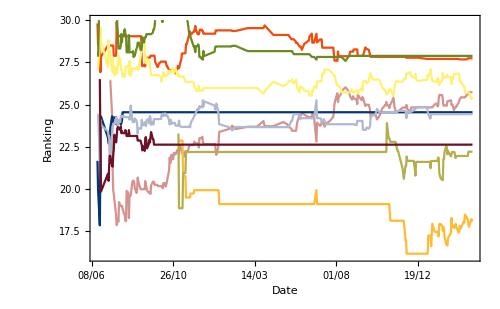
-Graphics- | TrueSkill Rating

 | CRSid | μ | ±σ
RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039] | nawb2 | 27.88 | ±1.13
RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744] | jc632 | 27.74 | ±1.13
RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902] | ao391 | 25.73 | ±1.2
RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076] | km558 | 25.45 | ±1.18
RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157] | nl263 | 24.54 | ±1.33
RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529] | ufk20 | 24.43 | ±1.12
RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392] | vvt20 | 22.62 | ±1.13
RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547] | mas259 | 22.21 | ±1.24
RGBColor[1., 0.7333333333333333, 0.2] | ka451 | 18.06 | ±1.28

Last Update:
2017-03-26

```mathematica
nameColor = AssociationThread[
showNames-> Flatten[ ColorData[#,"ColorList"]&/@{ 14,6,9,35} ]⟦;;Length[showNames]⟧
];

takeOnlyMu[dateAndTS_]:= {dateAndTS⟦1⟧, dateAndTS⟦2,1⟧}
takeMuSigma[dateAndTS_]:= {dateAndTS⟦1⟧, dateAndTS⟦2,1⟧,dateAndTS⟦2,2⟧}

removeInitial[list_]:= Select[ list, #⟦3⟧< 4.5 &]⟦All,{1,2}⟧

rankingsRange = {16, 30};

plotForPlayer[name_]:= DateListPlot[ 
removeInitial[ 
takeMuSigma/@(rankings⟦ All, {"Date", name}⟧[Values])    ],
PlotStyle->nameColor[name],
FrameLabel-> {"Date", "Ranking"},
FrameStyle->Directive[Black,FontSize-> 13],
DateTicksFormat->{"Day", "/","Month"},
PlotRange-> rankingsRange
]

plot =Show[
plotForPlayer/@ showNames,
ImageSize-> 500,
PlotRange-> rankingsRange
];



addStyle[line_]:= {
nameColor[line⟦1⟧] (*colour*), 
line⟦1⟧ (*name*),
Round[line⟦2⟧⟦1⟧, 0.01] (*mu*),
"±"<>ToString@Round[line⟦2⟧⟦2⟧, 0.01] (*sigma*)
} ;

leadTable = 
Column[{"TrueSkill Rating","",#, "", "Last Update:",DateString["ISODate"]}, Center] &@
Grid[{{"", "CRSid", "μ", "±σ"}} ~Join~
(addStyle/@
SortBy[ 
Transpose@{showNames , rankings⟦-1⟧/@showNames},
-#⟦2⟧⟦1⟧&])
];

out = Grid[{{plot, leadTable}}]
```

```mathematica
file = Export["/Users/kmisiunas/Dropbox/Public/foosball_trueskill_rankings.pdf", out];

Import["!/usr/local/bin/convert -density 200 '"<> file<> "' '"<> 
DirectoryName[file]<>FileBaseName[file]<>".png'", "Text"]
```

```mathematica
"!/usr/local/bin/convert -density 200 '"<> file<> "' '"<> 
DirectoryName[file]<>FileBaseName[file]<>".png'"
```

!/usr/local/bin/convert -density 200 '/Users/kmisiunas/Dropbox/Public/foosball_trueskill_rankings.pdf' '/Users/kmisiunas/Dropbox/Public/foosball_trueskill_rankings.png'

```mathematica
Import["!/usr/local/bin/convert -version", "Text"]
```

Version: ImageMagick 6.9.5-8 Q16 x86_64 2016-08-29 http://www.imagemagick.org
Copyright: Copyright (C) 1999-2016 ImageMagick Studio LLC
License: http://www.imagemagick.org/script/license.php
Features: Cipher DPC Modules 
Delegates (built-in): bzlib freetype jng jpeg ltdl lzma png tiff xml zlib

```mathematica
"/usr/local/bin/convert -density 200 '"<> file<> "' '"<> 
DirectoryName[file]<>FileBaseName[file]<>".png'"
```

/usr/local/bin/convert -density 200 '/Users/kmisiunas/Dropbox/Public/foosball_trueskill_rankings.pdf' '/Users/kmisiunas/Dropbox/Public/foosball_trueskill_rankings.png'

## Individual Reports

```mathematica
names
```

{ao391,ark44,atf29,eh443,jc632,jw870,ka451,km558,lw473,ma595,mas259,nawb2,nl263,oaa36,ojp25,rhp32,rjgs2,sp736,sw561,tj295,ufk20,vp341,vvt20}

```mathematica
user = "mas259";

width = 45;
```

```mathematica
(*show with style*)
Clear[printSt]
printSt[text_String]:= Style[ text, FontFamily->"Open Sans", FontSize->14]
printSt[num_?IntegerQ] := printSt[  ToString[num] ]
printSt[num_?NumberQ]:= printSt[ToString@NumberForm[num, {5,1}] ]
printSt[other_]:= other
```

```mathematica
(* basic analysis *)
userGames =  singles[Select[#"RedName" == user || #"BlueName" == user &]];
userNumber = userGames // Length;
userWon = userGames[ Select[#"RedName" == user  && #"RedScore" > #"BlueScore" ||
#"BlueName" == user  && #"RedScore" < #"BlueScore" &]];
userWonNumber = userWon // Length;
userLost = userGames[ Select[#"RedName" == user  && #"RedScore" < #"BlueScore" ||
#"BlueName" == user  && #"RedScore" > #"BlueScore" &]];
userLostNumber = userLost // Length;
userTotalScored = 
Total[ userGames[Select[#"RedName" == user &], "RedScore"] ] + Total[ userGames[Select[#"BlueName" == user &], "BlueScore"] ] ;
```

```mathematica
userOutBasic = Grid[Map[printSt,
{
{"Games Played:",userNumber},
{"Games Won:", userWonNumber},
{"", N[userWonNumber/ userNumber 100], "%"},
{"Games Lost:", userLostNumber},
{"", N[userLostNumber/ userNumber 100], "%"},
{"Goals scored:", userTotalScored},
{"Goals per game:", N[userTotalScored/userNumber]}
},
{2} ]
, Alignment->Left]
```

Games Played: | 29 | 
Games Won: | 11 | 
 | 37.9 | %
Games Lost: | 18 | 
 | 62.1 | %
Goals scored: | 245 | 
Goals per game: | 8.4 |

```mathematica
Unprotect[$TimeZone];
$TimeZone=1;
Protect[$TimeZone];
```

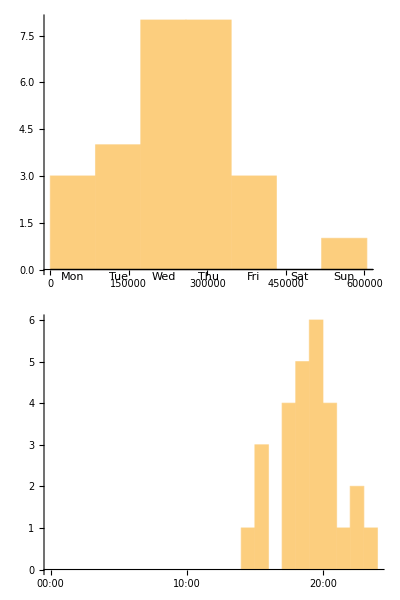

```mathematica
(*time histograms*)
neutraliseTimeZone[date_]:=DatePlus[date, Quantity[$TimeZone ,"Hour"]]

userDates =neutraliseTimeZone/@ Normal@
userGames[Select[ DateString[#Date, {"Second", "Millisecond"}]≠ "00000" &], "Date"];

userOutHist = Column[{
DateHistogram[Normal[userDates],"Day",DateReduction->"Week",
ImageSize->250, AspectRatio->1/2.6, TimeZone->$TimeZone],

DateHistogram[ TimeObject/@ Normal[userDates],"Hour",DateReduction->"Day",
ImageSize->250,AspectRatio->1/2.6, 
TimeZone->$TimeZone, DateTicksFormat->{"Hour24",":","Minute"}]
}]
```

```mathematica
(*color bias*)
userRed = userGames[ Select[#"RedName" == user  &]];
userBlue = userGames[ Select[#"BlueName" == user  &]];
userRedNumber = userRed// Length;
userBlueNumber = userBlue // Length;
userRedScored = Total@userRed[All,"RedScore"];
userBlueScored = Total@userBlue[All,"BlueScore"];
userRedWon = userRed[ Select[#"RedScore" > #"BlueScore"  &]];
userRedWonNumber = userRedWon // Length;
userBlueWon = userBlue[ Select[#"RedScore" < #"BlueScore"  &]];
userBlueWonNumber = userBlueWon // Length;
userColorBias =  (userBlueWonNumber/userBlueNumber)/(userRedWonNumber/userRedNumber )-0.5;
```

```mathematica
userOutColor = Grid[Map[printSt,
{
{"", "Red", HorizontalGauge[userColorBias, LabelStyle->Opacity[0],ScaleDivisions->4] ,"Blue"},
{"Games Played:",userRedNumber,"" ,userBlueNumber},
{"Games Won (%):",
 N[userRedWonNumber/userRedNumber 100],"", N[userBlueWonNumber/userBlueNumber 100] },
{"Goals per game:",  
N[userRedScored/userRedNumber ],"", N[userBlueScored/userBlueNumber ] }
},
{2} ]
, Alignment->Left]
```

| Red | -Graphics- | Blue
Games Played: | 16 |  | 13
Games Won (%): | 37.5 |  | 38.5
Goals per game: | 7.8 |  | 9.2

```mathematica
(*against other players*)

(* estimates p1 ranking *)
minGamesToAnalyse = 7;

(*old - slow or does not work*)
estimateRankingsFor2Players[games_, p1_, p2_]:= estimateRankings[games][All,p1]⟦-1,1⟧;

(*new and fast and simple *)
estimateRankingsFor2Players[games_, p1_, p2_]:= Length[games⟦-8;;⟧[ Select[#"RedName" == p1  && #"RedScore" > #"BlueScore" ||
#"BlueName" == p1  && #"RedScore" < #"BlueScore" &]]]/8.0;

estimatTrend[games_, p1_, p2_]:= estimateRankingsFor2Players[games⟦;;#⟧, p1, p2]&/@Reverse@Range[games//Length, 3, -5];

userVersus[player_]:= Module[
{games, gamesWon, gamesLost, trend},
games = userGames[Select[ #"RedName" == player || #"BlueName" == player &]];
If[minGamesToAnalyse > Length@games, Return[Nothing]  (*dont analyse*)];
gamesWon = games[ Select[#"RedName" == user  && #"RedScore" > #"BlueScore" ||
#"BlueName" == user  && #"RedScore" < #"BlueScore" &]];
gamesLost = games[ Select[#"RedName" == user  && #"RedScore" < #"BlueScore" ||
#"BlueName" == user  && #"RedScore" > #"BlueScore" &]];

trend = estimatTrend[games, user, player];

<| 
"Player" -> player,
"Games" -> Length@games,
"Games Won (%)"-> N[Length@gamesWon/ Length@games 100],
"Games Lost (%)"-> N[Length@gamesLost/ Length@games 100],
"Trend" ->
ListPlot[
trend,
Joined-> True,
(*AxesOrigin->{1,25},*)
PlotRange->{All,Automatic},
AxesStyle->Directive[ Black, Dashed],
Ticks->None,
Axes->{False,False},
PlotStyle->Orange,
ImageSize->80
]
|>
]
```

```mathematica
userVsOthers = SortBy[ userVersus/@ Complement[names,{user}]  , -#Games &];
```

```mathematica
titles = {"Player", "Games", "Games Won (%)", "Games Lost (%)","Trend"};

userOutOthers = Grid[Map[printSt,

{titles}~Join~(titles/.userVsOthers),

{2} ]
, Alignment->Center, Frame-> All, Background->{None, {LightOrange}}, ItemSize->(width*0.9)/5]
```

Player | Games | Games Won (%) | Games Lost (%) | Trend
km558 | 13 | 7.7 | 92.3 | -Graphics-
ka451 | 11 | 81.8 | 18.2 | -Graphics-

```mathematica
(*Styles*)
```

```mathematica
title[st_]:= Style[ st, FontFamily->"Open Sans", FontWeight->Bold, FontSize->28]
caption[st_]:= Grid[{{""},{ Style[ st, FontFamily->"Open Sans", FontSize->20] }},
 ItemSize->width, Alignment->Left, Dividers->{False, {3->True}}]
```

```mathematica
userReport = Column[{

"",title["Report for "<> user],
DateString["ISODate"],


caption["Statistics"],
Grid[{{ userOutBasic, userOutHist}}, ItemSize->width/2],
"",

caption["Color Preference"],
userOutColor,

caption[ "VS Other Players"],
userOutOthers


}, Alignment->Center]

Export["/Users/kmisiunas/Dropbox/Public/foosball_users/report_"<>user<>".pdf", userReport];
```

Report for mas259
2017-01-11

Statistics
Games Played: | 29 | 
Games Won: | 11 | 
 | 37.9 | %
Games Lost: | 18 | 
 | 62.1 | %
Goals scored: | 245 | 
Goals per game: | 8.4 |  | -Graphics-


Color Preference
 | Red | -Graphics- | Blue
Games Played: | 16 |  | 13
Games Won (%): | 37.5 |  | 38.5
Goals per game: | 7.8 |  | 9.2

VS Other Players
Player | Games | Games Won (%) | Games Lost (%) | Trend
km558 | 13 | 7.7 | 92.3 | -Graphics-
ka451 | 11 | 81.8 | 18.2 | -Graphics-

## Additional Manual analysis for Ulrich

```mathematica
userVersus2[player_]:= Module[
{games, gamesWon, gamesLost, trend},
games = userGames[Select[ #"Red Name" == player || #"Blue Name" == player &]];
If[0 > Length@games, Return[Nothing]  (*dont analyse*)];
gamesWon = games[ Select[#"Red Name" == user  && #"Red Score" > #"Blue Score" ||
#"Blue Name" == user  && #"Red Score" < #"Blue Score" &]];
gamesLost = games[ Select[#"Red Name" == user  && #"Red Score" < #"Blue Score" ||
#"Blue Name" == user  && #"Red Score" > #"Blue Score" &]];

trend = estimatTrend[games, user, player];

<| 
"Player" -> player,
"Games" -> Length@games,
"Games Won (%)"-> N[Length@gamesWon/ Length@games 100],
"Games Lost (%)"-> N[Length@gamesLost/ Length@games 100],
"Trend" ->
ListPlot[
trend,
Joined-> True,
AxesOrigin->{1,25},
PlotRange->{All,Automatic},
AxesStyle->Directive[ Black, Dashed],
Ticks->None,
Axes->{True,False},
PlotStyle->Orange,
ImageSize->80
]
|>
]
```

```mathematica
userVersus2["nl263"]
```

Power::infy: Infinite expression 1/0 encountered.

<|Player→nl263,Games→0,Games Won (%)→ComplexInfinity,Games Lost (%)→ComplexInfinity,Trend→-Graphics-|>

```mathematica
(("Games" * "Games Won (%)"/100)/.userVersus2["km558"])+
(("Games" * "Games Won (%)"/100)/.userVersus2["nawb2"])+
(("Games" * "Games Won (%)"/100)/.userVersus2["jc632"])
```

21.

```mathematica
colorBias = TimeSeries@Normal[{#Date,( #BlueScore-#RedScore )}&/@singles];
```

```mathematica
smooth=MovingMap[Mean,colorBias,{{3,"Month"}, Right,"Week"}];
```

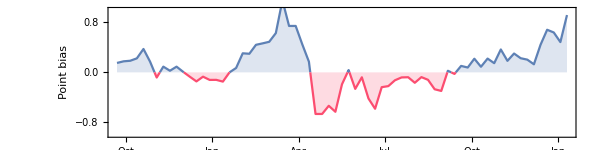

```mathematica
Show[
DateListPlot[smooth,
Filling-> Axis,
PlotRange->{0, All}
],
DateListPlot[smooth,
Filling-> Axis,
PlotStyle->RGBColor[0.99,0.3,0.44],
PlotRange->{All, 0}
],
PlotRange->{-1,1},
FrameStyle -> Directive[FontSize -> 11, Black],
AspectRatio -> 1/4,
ImageSize-> 600,
FrameLabel-> {None, "Point bias"}
]
```